```mathematica
(*mean loop length*)
loop = 100
```

100

```mathematica
(*mean gap length*)
gap=500
```

500

```mathematica
alpha= loop/gap
```

```mathematica
1
```

```mathematica
(*diffusivity of gap / diffusivity of loop; equals R=1 by default *)
```

```mathematica
R = 1
```

```mathematica
(*diagramm A*)
Ia[s_]:=1/s^(3/2)1/(alpha+1)(ⅇ^(-alpha×s)+√alpha s×NIntegrate[BesselI[1,2 ×s×√(alpha(1-x) x)]/((1-x) √x)ⅇ^(-x×s-alpha×(1-x)s),{x,0.0000,1},Exclusions->(1-x==0),Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"},MaxRecursion->100])
```

```mathematica
(*diagram B*)
Ib[s_]:=1/s^(3/2)alpha/(alpha+1)(s^2 NIntegrate[ⅇ^(-(t1+t2)s-alpha(1-t2)s)/(1-t2+R(t1×t2)/(t1+t2))^(3/2),{t1,0.0000001,+∞},{t2,0.00,1.0},Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"},MaxRecursion->100]+√alpha s^3 NIntegrate[((1-t2)(1-x)^(1/2)BesselI[1,2 s(1-t2)√(alpha(1-x) x)] ⅇ^(-(x+(1-x)alpha)(1-t2)s-(t1+t2)s))/(√x((1-t2)(1-x)+R(t1×t2)/(t1+t2))^(3/2)),{t1,0.0,100/s},{t2,0.0,1},{x,0.0,1},Exclusions->((1-t2)(1-x)+(t1×t2)/(t1+t2)==0),Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"},MaxRecursion->100])
```

```mathematica
(*diagram C*)
Ic[s_]:=1/s^(3/2)1/R^(3/2)alpha/(alpha+1)√π s^2×ⅇ^-s HypergeometricU[1/2,3,s]
```

```mathematica
(*diagram D*)
Id[s_]:=1/s^(3/2)alpha^2/(alpha+1)s^4(NIntegrate[((1-t2)^2(1-τ)ⅇ^(-alpha×τ(1-t2)s-(t1+t2+(1-t2)(1-τ)T)s))/((1-t2)τ+R(t1×t2)/(t1+t2)+R((1-t2)(1-τ)(T-1))/T)^(3/2),{t1,0.00001,+∞},{t2,0.00001,1},{τ,0.00001,1},{T,1.00001,+∞}]+√alpha s×NIntegrate[((1-t2)^3(1-τ)τ(1-x)^(1/2)x^(-1/2)×BesselI[1,2 s(1-t2)τ √(alpha(1-x) x)] ⅇ^(-alpha(1-x)τ(1-t2)s-x(1-t2)τ×s-(t1+t2+(1-t2)(1-τ)T)s))/((1-x)(1-t2)τ+R(t1×t2)/(t1+t2)+R((1-t2)(1-τ)(T-1))/T)^(3/2),{t1,0.00001,+∞},{t2,0.00001,1},{τ,0.00001,1},{x,0.00001,1},{T,1.00001,+∞}])
```

```mathematica
(*we will calculate contact probability in range [s_min,s_max]*)
Smin=0.1
Smax=100.0
```

0.1

100.

```mathematica
(*number of points*)
Ns=50
```

50

```mathematica
(*points are chosen from geometric progression with the ratio q*)
q=(Smax/Smin)^(1/(Ns-1))
```

1.1514

```mathematica
(*contact probability is determined by the sum of diagrams*)
Pcontact[s_]:=Ia[s]+Ic[s]+2Ib[s]+Id[s]
```

```mathematica
(*here we calculate contact probability*)
Contact=Table[{Smin×q^(n-1),Pcontact[Smin×q^(n-1)]},{n,Ns}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 56.0149 and 0.00233983 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.301407 and 0.0000658605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 42.6134 and 0.00108358 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.1,32.7758},{0.11514,26.7061},{0.132571,21.7881},{0.152642,17.8024},{0.175751,14.5712},{0.202359,11.9508},{0.232995,9.82426},{0.26827,8.09727},{0.308884,6.69315},{0.355648,5.5498},{0.409492,4.61685},{0.471487,3.85347},{0.542868,3.22657},{0.625055,2.70935},{0.719686,2.28019},{0.828643,1.9217},{0.954095,1.62},{1.09854,1.3641},{1.26486,1.14544},{1.45635,0.957473},{1.67683,0.795292},{1.9307,0.655307},{2.223,0.53492},{2.55955,0.43221},{2.94705,0.345648},{3.39322,0.273839},{3.90694,0.21534},{4.49843,0.168569},{5.17947,0.131804},{5.96362,0.103274},{6.86649,0.0812797},{7.90604,0.064323},{9.10298,0.0511752},{10.4811,0.0408926},{12.0679,0.0327809},{13.895,0.0263367},{15.9986,0.021192},{18.4207,0.0170712},{21.2095,0.0137632},{24.4205,0.0111035},{28.1177,0.00896243},{32.3746,0.00723732},{37.2759,0.00584631},{42.9193,0.00472403},{49.4171,0.00381813},{56.8987,0.00308658},{65.5129,0.00249563},{75.4312,0.00201811},{86.8511,0.00163217},{100.,0.00132018}}

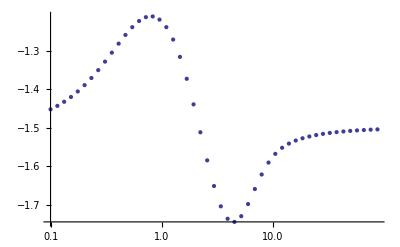

```mathematica
(*here we plot the log-derivative of the contact probability*)
ListLogLinearPlot[Table[{Part[Part[Contact,n],1],Log10[Part[Part[Contact,n+1],2]/Part[Part[Contact,n],2]]/Log10[Part[Part[Contact,n+1],1]/Part[Part[Contact,n],1]]},{n,Ns-1}]]
```